```mathematica
(*
MIT License

Copyright (c) 2020 Utkarsh Priyam

Permission is hereby granted,free of charge,to any person obtaining a copy
of this software and associated documentation files (the "Software"),to deal
in the Software without restriction,including without limitation the rights
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell
copies of the Software,and to permit persons to whom the Software is
furnished to do so,subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND,EXPRESS OR
IMPLIED,INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
LIABILITY,WHETHER IN AN ACTION OF CONTRACT,TORT OR OTHERWISE,ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.
*)
```

# Shuffling/Perfect (Faro) Shuffles

## Shuffle Functions (Do NOT Modify)

```mathematica
outshuffle[deck_]:=(
numCards=Dimensions[deck][[1]];
If[numCards==1,Return[deck]];
tempCount=Floor[numCards/2];
newDeck=deck;
If[numCards≠2tempCount,newDeck=Append[newDeck,0];tempCount++];
partition=Partition[newDeck,tempCount];
first=partition[[1]];
second=partition[[2]];
newDeck={};
For[i=1,i≤tempCount,i++,newDeck=Append[Append[newDeck,first[[i]]],second[[i]]]];
If[numCards≠2tempCount,newDeck=Delete[newDeck,numCards+1]];
newDeck
)
inshuffle[deck_]:=(
numCards=Dimensions[deck][[1]];
If[numCards==1,Return[deck]];
tempCount=Floor[numCards/2];
partition=Partition[deck,tempCount];
first=partition[[1]];
second=partition[[2]];
newDeck={};
For[i=1,i≤tempCount,i++,newDeck=Append[Append[newDeck,second[[i]]],first[[i]]]];
If[numCards≠2tempCount,newDeck=Append[newDeck,deck[[numCards]]]];
newDeck
)
shuffle[deck_]:=inshuffle[deck]
countShuffles[deck_]:=(
count=1;
newDeck=shuffle[deck];
While[deck≠newDeck,newDeck=shuffle[newDeck];count++];
count
)
```

## Count Shuffles

### Data Input (Search Bound)

```mathematica
upperBound=20;
```

### Search and Catalog (Do NOT Modify)

Number of Cards | Number of Inshuffles | Number of Outshuffles
1 | 1 | 1
2 | 2 | 1
3 | 2 | 2
4 | 4 | 2
5 | 4 | 4
6 | 3 | 4
7 | 3 | 3
8 | 6 | 3
9 | 6 | 6
10 | 10 | 6
11 | 10 | 10
12 | 12 | 10
13 | 12 | 12
14 | 4 | 12
15 | 4 | 4
16 | 8 | 4
17 | 8 | 8
18 | 18 | 8
19 | 18 | 18
20 | 6 | 18

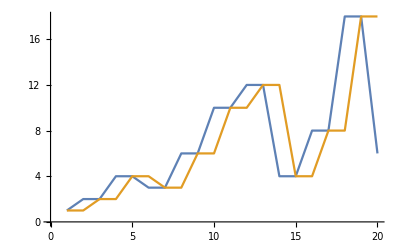

```mathematica
shuffle[deck_]:=inshuffle[deck];
ins=Table[countShuffles[Table[k,{k,n}]],{n,1,upperBound}];
shuffle[deck_]:=outshuffle[deck];
outs=Table[countShuffles[Table[k,{k,n}]],{n,1,upperBound}];
shuffleCounts=Table[{n,ins[[n]],outs[[n]]},{n,1,upperBound}];Prepend[shuffleCounts,{"Number of Cards", "Number of Inshuffles", "Number of Outshuffles"}]//TableForm
ListLinePlot[{Table[{x,ins[[x]]},{x,1,upperBound}],Table[{x,outs[[x]]},{x,1,upperBound}]}]
```